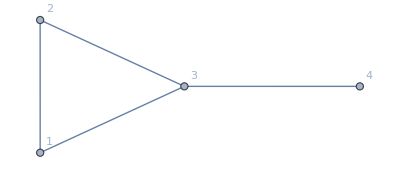

```mathematica
g=Graph[{1<->2,1<->3,2<->3,3<->4},VertexLabels->"Name"]
```

```mathematica
ChromaticPolynomial[g,x]
```

-2 x+5 x^2-4 x^3+x^4

```mathematica
FindFullFormula[g]
```

{v1x2x3x4,v1x24x3,v14x2x3}

```mathematica
SymmetricPolynomial[1,Table[Indexed[x,i],{i,4}]]
```

x1+x2+x3+x4

```mathematica
GraphAutomorphismGroup[g]
```

PermutationGroup[{Cycles[{{1,2}}]}]

```mathematica
Det[Table[Indexed[a,i],{i,BellB[4]}]MobiusMatrix[allGraphs4]]
```

a1 a2 a3 a4 a5 a6 a7 a8 a9 a10 a11 a12 a13 a14 a15

```mathematica
Inverse[MobiusMatrix[allGraphs4]]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,0,0,0,0,0,1,0,0,1,0,0,1,1},{0,0,1,0,0,0,0,0,0,1,1,1,0,0,1},{0,0,0,1,0,0,0,0,1,0,1,0,1,0,1},{0,0,0,0,1,0,0,1,0,0,0,1,1,0,1},{0,0,0,0,0,1,0,0,1,0,0,1,0,1,1},{0,0,0,0,0,0,1,0,0,1,0,0,1,1,1},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
m=Table[Indexed[a,i],{i,BellB[4]}]Inverse[MobiusMatrix[allGraphs4]];MatrixForm[m]
```

(a1 | a1 | a1 | a1 | a1 | a1 | a1 | a1 | a1 | a1 | a1 | a1 | a1 | a1 | a1
0 | a2 | 0 | 0 | 0 | 0 | 0 | a2 | 0 | 0 | a2 | 0 | 0 | a2 | a2
0 | 0 | a3 | 0 | 0 | 0 | 0 | 0 | 0 | a3 | a3 | a3 | 0 | 0 | a3
0 | 0 | 0 | a4 | 0 | 0 | 0 | 0 | a4 | 0 | a4 | 0 | a4 | 0 | a4
0 | 0 | 0 | 0 | a5 | 0 | 0 | a5 | 0 | 0 | 0 | a5 | a5 | 0 | a5
0 | 0 | 0 | 0 | 0 | a6 | 0 | 0 | a6 | 0 | 0 | a6 | 0 | a6 | a6
0 | 0 | 0 | 0 | 0 | 0 | a7 | 0 | 0 | a7 | 0 | 0 | a7 | a7 | a7
0 | 0 | 0 | 0 | 0 | 0 | 0 | a8 | 0 | 0 | 0 | 0 | 0 | 0 | a8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a9 | 0 | 0 | 0 | 0 | 0 | a9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a10 | 0 | 0 | 0 | 0 | a10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a11 | 0 | 0 | 0 | a11
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a12 | 0 | 0 | a12
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a13 | 0 | a13
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a14 | a14
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a15)

```mathematica
Det[m]
```

a1 a2 a3 a4 a5 a6 a7 a8 a9 a10 a11 a12 a13 a14 a15

```mathematica
m=(ConversionMatrix["E","C"]//Inverse)Table[Indexed[a,i],{i,BellB[5]}];MatrixForm[m]
```

(a1 | -a1 | -a1 | -a1 | -a1 | -a1 | -a1 | -a1 | -a1 | -a1 | -a1 | a1 | a1 | a1 | a1 | a1 | a1 | a1 | a1 | a1 | a1 | a1 | a1 | a1 | a1 | a1 | 2 a1 | 2 a1 | 2 a1 | 2 a1 | 2 a1 | 2 a1 | 2 a1 | 2 a1 | 2 a1 | 2 a1 | -2 a1 | -2 a1 | -2 a1 | -2 a1 | -2 a1 | -2 a1 | -2 a1 | -2 a1 | -2 a1 | -2 a1 | -6 a1 | -6 a1 | -6 a1 | -6 a1 | -6 a1 | 24 a1
0 | a2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a2 | 0 | 0 | -a2 | 0 | 0 | -a2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a2 | 0 | 0 | -a2 | 0 | 0 | 0 | 0 | 0 | -a2 | a2 | 2 a2 | 0 | 0 | a2 | 0 | 0 | 0 | a2 | 0 | 2 a2 | 0 | 0 | 2 a2 | 2 a2 | -6 a2
0 | 0 | a3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a3 | 0 | -a3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a3 | 0 | 0 | -a3 | -a3 | 0 | 0 | 0 | 0 | 0 | -a3 | 0 | 0 | a3 | 0 | 0 | 2 a3 | 0 | a3 | 0 | 0 | 0 | a3 | 2 a3 | 2 a3 | 0 | 0 | 2 a3 | -6 a3
0 | 0 | 0 | a4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a4 | 0 | 0 | 0 | -a4 | 0 | 0 | 0 | -a4 | 0 | 0 | 0 | 0 | 0 | -a4 | 0 | -a4 | 0 | 0 | 0 | 0 | 0 | -a4 | 0 | a4 | 0 | 2 a4 | 0 | 0 | 0 | a4 | a4 | 0 | 0 | 2 a4 | 0 | 2 a4 | 0 | 2 a4 | -6 a4
0 | 0 | 0 | 0 | a5 | 0 | 0 | 0 | 0 | 0 | 0 | -a5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a5 | 0 | 0 | -a5 | 0 | 0 | -a5 | -a5 | 0 | -a5 | 0 | 0 | 0 | 0 | 0 | 0 | a5 | 0 | 0 | 0 | 0 | 0 | a5 | 2 a5 | a5 | 2 a5 | 2 a5 | 2 a5 | 0 | 0 | -6 a5
0 | 0 | 0 | 0 | 0 | a6 | 0 | 0 | 0 | 0 | 0 | 0 | -a6 | 0 | 0 | 0 | 0 | 0 | -a6 | 0 | 0 | 0 | 0 | 0 | 0 | -a6 | 0 | -a6 | 0 | -a6 | 0 | -a6 | 0 | 0 | 0 | 0 | 0 | 0 | a6 | 0 | a6 | 0 | 2 a6 | 0 | 0 | a6 | 2 a6 | 2 a6 | 0 | 2 a6 | 0 | -6 a6
0 | 0 | 0 | 0 | 0 | 0 | a7 | 0 | 0 | 0 | 0 | 0 | 0 | -a7 | 0 | 0 | 0 | 0 | 0 | -a7 | 0 | 0 | -a7 | 0 | 0 | 0 | 0 | 0 | -a7 | -a7 | 0 | 0 | -a7 | 0 | 0 | 0 | 0 | 0 | 0 | a7 | a7 | 2 a7 | 0 | a7 | 0 | 0 | 2 a7 | 0 | 2 a7 | 2 a7 | 0 | -6 a7
0 | 0 | 0 | 0 | 0 | 0 | 0 | a8 | 0 | 0 | 0 | 0 | 0 | 0 | -a8 | -a8 | -a8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a8 | -a8 | -a8 | 0 | 0 | 0 | 2 a8 | a8 | a8 | a8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 a8 | 2 a8 | 2 a8 | 0 | -6 a8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a9 | -a9 | -a9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a9 | 0 | 0 | -a9 | -a9 | 0 | 0 | a9 | 0 | 0 | 2 a9 | a9 | a9 | 0 | 0 | 0 | 0 | 2 a9 | 2 a9 | 0 | 2 a9 | -6 a9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a10 | -a10 | -a10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a10 | 0 | -a10 | 0 | -a10 | 0 | 0 | a10 | 0 | 0 | a10 | 0 | 2 a10 | a10 | 0 | 0 | 2 a10 | 0 | 2 a10 | 2 a10 | -6 a10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a11 | -a11 | -a11 | 0 | 0 | 0 | 0 | 0 | 0 | -a11 | 0 | -a11 | -a11 | 0 | 0 | 0 | a11 | 0 | 0 | a11 | 0 | a11 | 2 a11 | 0 | 0 | 2 a11 | 2 a11 | 2 a11 | -6 a11
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a12 | 0 | 0 | 0 | 0 | 0 | 0 | -a12 | 0 | -a12 | 0 | 0 | 0 | 0 | 2 a12
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a13 | 0 | 0 | 0 | -a13 | 0 | 0 | 0 | -a13 | 0 | 0 | 0 | 0 | 2 a13
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a14 | 0 | -a14 | 0 | 0 | 0 | 0 | -a14 | 0 | 0 | 0 | 0 | 2 a14
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a15 | -a15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a15 | 0 | 2 a15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a16 | 0 | 0 | -a16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a16 | 0 | 0 | 0 | 2 a16
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a17 | 0 | -a17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a17 | 0 | 0 | 2 a17
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a18 | 0 | 0 | -a18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a18 | 2 a18
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a19 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a19 | 0 | -a19 | 0 | 0 | 0 | 0 | -a19 | 0 | 0 | 0 | 2 a19
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a20 | -a20 | 0 | 0 | 0 | 0 | 0 | 0 | -a20 | 0 | 0 | 2 a20
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a21 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a21 | 0 | 0 | 0 | 0 | -a21 | 0 | 0 | 0 | 0 | 0 | 0 | -a21 | 2 a21
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a22 | -a22 | 0 | 0 | -a22 | 0 | 0 | 0 | 2 a22
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a23 | 0 | -a23 | 0 | 0 | 0 | 0 | 0 | -a23 | 0 | 2 a23
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a24 | 0 | 0 | 0 | 0 | 0 | -a24 | 0 | 0 | 0 | 0 | -a24 | 2 a24
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a25 | -a25 | 0 | 0 | -a25 | 0 | 0 | 2 a25
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a26 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a26 | 0 | 0 | -a26 | 0 | 0 | 0 | -a26 | 0 | 2 a26
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a27 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a27 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a27 | 0 | 0 | 0 | -a27 | 2 a27
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a28 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a28 | -a28 | -a28 | 0 | 0 | 0 | 2 a28
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a29 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a29 | 0 | 0 | -a29 | 0 | -a29 | 0 | 0 | 2 a29
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a30 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a30 | 0 | 0 | 0 | 0 | 0 | -a30 | 0 | 0 | -a30 | 0 | 2 a30
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a31 | 0 | 0 | 0 | 0 | 0 | 0 | -a31 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a31 | -a31 | 0 | 0 | 2 a31
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a32 | 0 | 0 | 0 | 0 | 0 | 0 | -a32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a32 | 0 | -a32 | 0 | 2 a32
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a33 | 0 | 0 | 0 | 0 | 0 | 0 | -a33 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a33 | -a33 | 0 | 2 a33
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a34 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a34 | 0 | 0 | 0 | 0 | 0 | -a34 | 0 | 0 | -a34 | 2 a34
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a35 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a35 | 0 | 0 | 0 | 0 | 0 | -a35 | 0 | -a35 | 2 a35
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a36 | 0 | 0 | 0 | 0 | -a36 | -a36 | 2 a36
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a37 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a37
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a38 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a38
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a39 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a39
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a40 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a40
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a41 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a41
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a42 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a42
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a43 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a43
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a44 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a44
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a45 | 0 | 0 | 0 | 0 | 0 | 0 | -a45
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a46 | 0 | 0 | 0 | 0 | 0 | -a46
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a47 | 0 | 0 | 0 | 0 | -a47
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a48 | 0 | 0 | 0 | -a48
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a49 | 0 | 0 | -a49
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a50 | 0 | -a50
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a51 | -a51
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a52)

```mathematica
Det[m]
```

a1 a2 a3 a4 a5 a6 a7 a8 a9 a10 a11 a12 a13 a14 a15 a16 a17 a18 a19 a20 a21 a22 a23 a24 a25 a26 a27 a28 a29 a30 a31 a32 a33 a34 a35 a36 a37 a38 a39 a40 a41 a42 a43 a44 a45 a46 a47 a48 a49 a50 a51 a52

```mathematica
Table[{base1,base2,ConversionMatrix[base1,base2]//Det},{base1,allBases},{base2,allBases}]
```

{{{C,C,1},{C,E,1},{C,G,1},{C,F,-1/195689447424},{C,T,1}},{{E,C,1},{E,E,1},{E,G,1},{E,F,-1/195689447424},{E,T,1}},{{G,C,1},{G,E,1},{G,G,1},{G,F,-1/195689447424},{G,T,1}},{{F,C,-195689447424},{F,E,-195689447424},{F,G,-195689447424},{F,F,1},{F,T,-195689447424}},{{T,C,1},{T,E,1},{T,G,1},{T,F,-1/195689447424},{T,T,1}}}

```mathematica
FactorInteger[195689447424]
```

{{2,28},{3,6}}

```mathematica
allGraphs4FakeAtomKeys
```

{0,243,364,333,273,244,81,109,84,27,36,9,13,3,1}

```mathematica
Bases["F"]=Association[]
```

<||>

```mathematica
Bases["F","Colofour"]="colofournull"
```

colofournull

```mathematica
Bases["F","AtomKeys"]=allGraphs4FakeAtomKeys
```

{0,243,364,333,273,244,81,109,84,27,36,9,13,3,1}

```mathematica
Bases["F","Variables"]=Table[allGraphs4[k,"colofournull"],{k,allGraphs4FakeAtomKeys}]
```

{p1x2x3x4,p12x3x4,p1234,p123x4,p124x3,p12x34,p13x2x4,p134x2,p13x24,p14x2x3,p14x23,p1x23x4,p1x234,p1x24x3,p1x2x34}

```mathematica
AppendTo[allBases,"F"]
```

{C,E,G,F}

```mathematica
Bases
```

<|C→<|Colofour→colofour,AtomKeys→{364,365,373,367,607,445,391,608,448,400,377,697,637,473,728},Variables→{v1x2x3x4,v1x2x34,v1x23x4,v1x24x3,v12x3x4,v13x2x4,v14x2x3,v12x34,v13x24,v14x23,v1x234,v123x4,v124x3,v134x2,v1234}|>,E→<|Colofour→colofourrealnull,AtomKeys→{0,2,18,6,486,162,54,488,168,72,26,666,546,218,728},Variables→{n1x2x3x4,n1x2x34,n1x23x4,n1x24x3,n12x3x4,n13x2x4,n14x2x3,n12x34,n13x24,n14x23,n1x234,n123x4,n124x3,n134x2,n1234}|>,G→<|Colofour→colofourgenerator,AtomKeys→{364,363,355,361,121,283,337,120,280,328,351,31,91,255,0},Variables→{g1x2x3x4,g1x2x34,g1x23x4,g1x24x3,g12x3x4,g13x2x4,g14x2x3,g12x34,g13x24,g14x23,g1x234,g123x4,g124x3,g134x2,g1234}|>,F→<|Colofour→colofournull,AtomKeys→{0,243,364,333,273,244,81,109,84,27,36,9,13,3,1}|>|>

```mathematica
Table[{base1,base2,ConversionMatrix[base1,base2]//Det},{base1,allBases},{base2,allBases}]
```

{{{C,C,1},{C,E,1},{C,G,1},{C,F,-1/96}},{{E,C,1},{E,E,1},{E,G,1},{E,F,-1/96}},{{G,C,1},{G,E,1},{G,G,1},{G,F,-1/96}},{{F,C,-96},{F,E,-96},{F,G,-96},{F,F,1}}}

```mathematica
FactorInteger[96]
```

{{2,5},{3,1}}

```mathematica
EulerPhi[195689447424]
```

65229815808

```mathematica
FactorInteger[65229815808]
```

{{2,28},{3,5}}

```mathematica
FactorInteger[195689447424]
```

{{2,28},{3,6}}

```mathematica
EulerPhi[96]
```

32

```mathematica
Select[Range[10000],EulerPhi[#]*3==#&]
```

{6,12,18,24,36,48,54,72,96,108,144,162,192,216,288,324,384,432,486,576,648,768,864,972,1152,1296,1458,1536,1728,1944,2304,2592,2916,3072,3456,3888,4374,4608,5184,5832,6144,6912,7776,8748,9216}